```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
```

```mathematica
Pestablish[Ne_,s_,p0_]:=(1-Exp[-4Ne s p0])/(1-Exp[-4Ne s])
```

```mathematica
FinalFreq[x0_,s_,t_]:=x0 Exp[s*t]; (* Simplest model *)
Detected[x0_,s_,t_,Thresh_]:=If[FinalFreq[x0,s,t]>=Thresh,1,0]; (* Just checking for being larger than the threshold, given x0. *)
```

```mathematica
PDetect[Ne_,s_,p0_,gens_]:=Module[{tmp, thresh, Thresh},
tmp = Integrate[Evaluate[Kimura[p0,y,gens/(2 Ne),100]],{y, Ψ,1}];
thresh = NSolve[tmp == 0.01&& 0<Ψ<1, {Ψ}, Reals] //Flatten;
Thresh = Ψ/.thresh;
Pestablish[Ne,s,p0] Integrate[
PDF[ExponentialDistribution[1/(p0/Pestablish[Ne,s,p0])],x0]
Detected[x0,s,gens,Thresh],
{x0,0,Infinity}]
]
```

```mathematica
(* Logistic function for selection, rather than exponential: *)
```

```mathematica
FinalFreqLogistic[x0_,s_,t_]:=x0 Exp[s t]/(1+x0(Exp[s t] - 1));
DetectedLogistic[x0_,s_,t_,Thresh_]:=If[FinalFreqLogistic[x0,s,t]>=Thresh,1,0]; 
PDetectLogistic[Ne_,s_,p0_,gens_]:=Module[{tmp, thresh, Thresh},
tmp = Integrate[Evaluate[Kimura[p0,y,gens/(2 Ne),100]],{y, Ψ,1}];
thresh = NSolve[tmp == 0.01&& 0<Ψ<1, {Ψ}, Reals] //Flatten;
Thresh = Ψ/.thresh;
Pestablish[Ne,s,p0] Integrate[
PDF[ExponentialDistribution[1/(p0/Pestablish[Ne,s,p0])],x0]
DetectedLogistic[x0,s,gens,Thresh],
{x0,0,Infinity}]
]
```

```mathematica
PDetectNGenic[Ne_,s_,p0_,gens_] :=Module[{tmp, thresh, Thresh,init, soln},
tmp = Integrate[Evaluate[Kimura[p0,y,gens/(2 Ne),100]],{y, Ψ,1}];
thresh = NSolve[tmp == 0.01&& 0<Ψ<1, {Ψ}, Reals] //Flatten;
Thresh = Ψ/.thresh;
init = Evaluate[PDF[TriangularDistribution[{(p0 - 1/(2 Ne)),(p0 + 1/(2 Ne))},p0],x]];
soln=NDSolve[
{D[u[t,x],t]==D[x(1-x)/2 u[t,x],x,x]-2 Ne s D[x(1-x)u[t,x],x],
u[0,x]==init},
u,{t,0,0.5},{x,0,1}, MaxStepSize->.00025
];
NIntegrate[Evaluate[{u[gens/(2 Ne), x]} /. soln],{x,Thresh,1}][[1]][[1]]
]
```

```mathematica
PDetect[500,0.01,0.1,100]
```

0.252269

```mathematica
PDetectLogistic[500,0.01,0.1,100]
```

0.16922

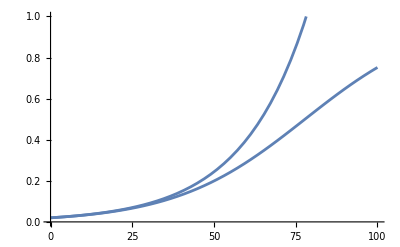

```mathematica
Plot[
{FinalFreq[x0,s,t],
FinalFreqLogistic[x0,s,t]}/.{s->0.05,x0->0.02},
{t,0,100},
PlotRange->{0,1}]
```

```mathematica
Do[Clear[p1,p2];
p1 = PDetect[500,selCoef,0.1,50];
p2 = PDetectLogistic[500,selCoef,0.1,50];
Export[StringJoin["pDetection_heur","s",ToString[selCoef],".csv"], {{selCoef,p1,p2}}, "csv"],
{selCoef, {0,0.001,0.005,0.01,0.015,0.02}}
]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

ExponentialDistribution::posprm: Parameter Indeterminate at position 1 in ExponentialDistribution[Indeterminate] is expected to be positive.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ExponentialDistribution::posprm: Parameter Indeterminate at position 1 in ExponentialDistribution[Indeterminate] is expected to be positive.

```mathematica
Do[Clear[p1,p2];
p1 = PDetect[500,0.01,0.1,time];
p2 = PDetectLogistic[500,0.01,0.1,time];
Export[StringJoin["pDetection_heur_","time",ToString[time],".csv"], {{time,p1,p2}}, "csv"],
{time, {50,100,150,200}}
]
```

General::munfl: Exp[-712.95] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.65] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-742.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Do[Clear[p1,p2];
p1 = PDetect[500,0.01,start,50];
p2 = PDetectLogistic[500,0.01,start,50];
Export[StringJoin["pDetection_heur_","start",ToString[start],".csv"], {{start,p1,p2}}, "csv"],
{start, {0.025,0.05,0.1,0.15,0.2}}
]
```

```mathematica
Do[Clear[p1,p2,pnum];
p1 = PDetect[500,selCoef,0.1,50];
p2 = PDetectLogistic[500,selCoef,0.1,50];
pnum = PDetectNGenic[500, selCoef, 0.1,50];
Export[StringJoin["pDetection_heur","genic",ToString[selCoef],".csv"], {{selCoef,p1,p2,pnum}}, "csv"],
{selCoef, {0.001,0.005,0.01,0.015,0.02, 0.05,0.1}}
]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

General::stop: Further output of NDSolve::bcart will be suppressed during this calculation.